```mathematica
VelocityField[x_, z_, d_,k_, σ_]:=(2 k (x z Cos[(2 d k x z)/(z^2+4 k^2 σ^4)]+x z Cosh[(4 d k^2 x σ^2)/(z^2+4 k^2 σ^4)]-2 d k σ^2 Sin[(2 d k x z)/(z^2+4 k^2 σ^4)]-d z Sinh[(4 d k^2 x σ^2)/(z^2+4 k^2 σ^4)]))/((z^2+4 k^2 σ^4) (Cos[(2 d k x z)/(z^2+4 k^2 σ^4)]+Cosh[(4 d k^2 x σ^2)/(z^2+4 k^2 σ^4)]))
```

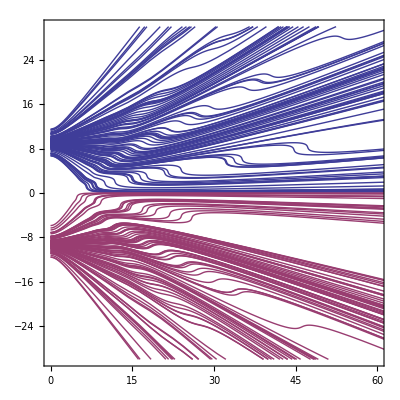

```mathematica
ddd = 9.0;
σσσ = 1.0;
kkk = 1.0;
HollandtablU=Table[NDSolve[{D[y[t], t]==1/(2 kkk)VelocityField[y[t], t, ddd,kkk, σσσ ],y[0]== ddd+ RandomVariate[NormalDistribution[0, σσσ]]},y,{t,0,100}],{100}];
HollandtablD=Table[NDSolve[{D[y[t],t]==1/(2 kkk)VelocityField[y[t], t, ddd,kkk, σσσ ],y[0]== -ddd+RandomVariate[NormalDistribution[0, σσσ]]},y,{t,0,100}],{100}];
Plot[{y[t]/.HollandtablU,y[t]/.HollandtablD},{t,0,100}, PlotRange->{{0,60},{-30,30}},Frame->True,Axes->True,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

```mathematica
ddd = 9.0;
σσσ = 1.0;
www = 1.0;
kkk= 1.0;
tmax = 70.0;
CHUNK = 100;
REPEAT = 100;
CUTTOFF = 40.0;

outstream=OpenAppend["BohmianDataDoubleSlit7.dat"];

Do[
Parallelize[
Hollandtabl3DU=Table[NDSolve[{D[y[t], t]==1/(2 kkk)VelocityField[y[t], t, ddd,kkk, σσσ ],y[0]== ddd+RandomVariate[NormalDistribution[0, σσσ]]},y,{t,0,tmax}],{CHUNK}];
Hollandtabl3DD=Table[NDSolve[{D[y[t], t]==1/(2 kkk)VelocityField[y[t], t, ddd,kkk, σσσ ],y[0]== -ddd+RandomVariate[NormalDistribution[0, σσσ]]},y,{t,0,tmax}],{CHUNK}];
];

TestTableXU[t_] = Flatten[y[t]/.Hollandtabl3DU];
TestTableXD[t_] = Flatten[y[t]/.Hollandtabl3DD];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt+=0.1, If[(TestTableXU[ttt][[NNN]]^2+(ttt)^2)>=CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableXU[ttt][[NNN]]/(ttt)]];Break[]]]
For[ttt=30,ttt < tmax, ttt+=0.1, If[(TestTableXD[ttt][[NNN]]^2+(ttt)^2)>=CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableXD[ttt][[NNN]]/(ttt)]];Break[]]]
];

Export[outstream,HistTableAngle];

WriteString[outstream,"\n"]
,{REPEAT}];

Close[outstream]
```

$Aborted

BohmianDataDoubleSlit6.dat

```mathematica
Variance[ReadDataSingle]
```

0.221225

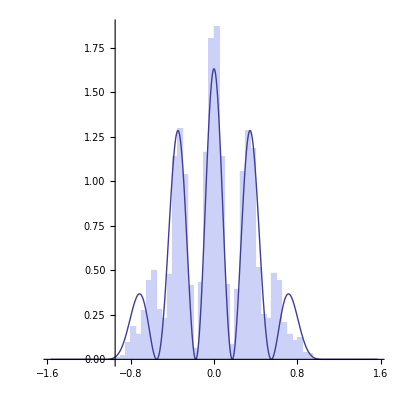

```mathematica
ReadDataSingle = Flatten[Import["BohmianDataDoubleSlit6.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[{1.8(ⅇ^(-Sec[x]^2/0.75^2))/(π Erfc[1/0.75])Cos[9Sin[x]]^2},{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

```mathematica
ddd = 9.0;
σσσ = 1.0;
www = 1.0;
kkk= 1.0;
tmax = 70.0;
CHUNK = 100;
REPEAT = 10;
CUTTOFF = 40.0;

outstream=OpenAppend["BohmianDataDoubleSlit7.dat"];

Do[
Parallelize[
Hollandtabl3DU=Table[NDSolve[{D[y[t], t]==1/(2 kkk)VelocityField[y[t], t, ddd,kkk, σσσ ],y[0]== ddd+RandomVariate[UniformDistribution[{-2σσσ,2 σσσ}]]},y,{t,0,tmax}],{CHUNK}];
Hollandtabl3DD=Table[NDSolve[{D[y[t], t]==1/(2 kkk)VelocityField[y[t], t, ddd,kkk, σσσ ],y[0]== -ddd+RandomVariate[UniformDistribution[{-2σσσ,2 σσσ}]]},y,{t,0,tmax}],{CHUNK}];
];

TestTableXU[t_] = Flatten[y[t]/.Hollandtabl3DU];
TestTableXD[t_] = Flatten[y[t]/.Hollandtabl3DD];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt+=0.1, If[(TestTableXU[ttt][[NNN]]^2+(ttt)^2)>=CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableXU[ttt][[NNN]]/(ttt)]];Break[]]]
For[ttt=30,ttt < tmax, ttt+=0.1, If[(TestTableXD[ttt][[NNN]]^2+(ttt)^2)>=CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableXD[ttt][[NNN]]/(ttt)]];Break[]]]
];

Export[outstream,HistTableAngle];

WriteString[outstream,"\n"]
,{REPEAT}];

Close[outstream]
```

BohmianDataDoubleSlit7.dat

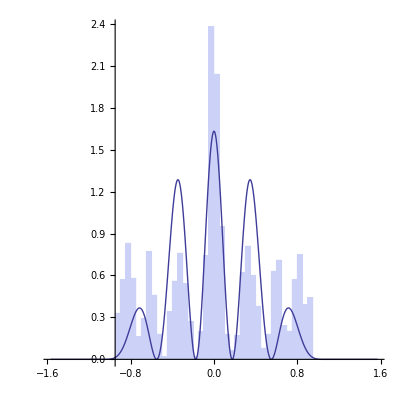

```mathematica
ReadDataSingle = Flatten[Import["BohmianDataDoubleSlit7.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[{1.8(ⅇ^(-Sec[x]^2/0.75^2))/(π Erfc[1/0.75])Cos[9Sin[x]]^2},{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```